```mathematica
afun=(GG^(1/3) (( m1+m2) )^(1/3))/((f)^(2/3) π^(2/3));
```

```mathematica
Rsol=6.995 10^10;
Msol = 2 10^33;
Mchirpf[m11_,m22_]=(m11 m22)^(3/5)/(m11+m22)^(1/5);
G = 6.67 10^-8;
c = 3 10^10
k1 = 0.143;
Q=5 10^8;
c = 3 10^10;
Msol = 2 10^33;
mHz = 0.001;
kK4 =10^4;
σ = 5.67 10^-5;
rg2=0.1;
```

30000000000

## Figure 1 : mass radius relation

```mathematica
labels=Directive[FontSize->18,FontFamily->"Times",Black];
```

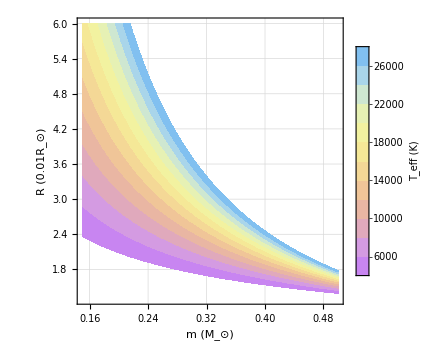

```mathematica
contourprim= ContourPlot[(1.1798232975286564*^47 Log[mmm]^2-1.4023785637137418*^48 Log[mmm] Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]+4.167288525500679*^48 Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]^2)/(7.70388920852663*^43+3.4482434674930335*^44 Log[mmm]+3.858565034251842*^44 Log[mmm]^2) ,{mmm,0.15,0.5},{rr,1.3,6},Contours-> {1,4000,6000,8000,10000,12000,14000,16000,18000,20000,22000,24000,26000,28000},ImageSize-> Medium,ColorFunction->"Pastel", Axes-> True,FrameLabel->{Style["m (M_⊙)",20,Black],Style["R (0.01R_⊙)",20,Black]},FrameTicksStyle->Directive[FontSize->20,Black],ContourStyle->None,ScalingFunctions->{None,None},BaseStyle->{FontSize->20},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["T_eff (K)",Black],LabelStyle->labels],{After,Top}],PlotRange->{{0.15,0.5},{1.3,6},{4000,28000}},LabelStyle->(FontFamily->"Times"),GridLines->Automatic
]
```

```mathematica
cplot1=ContourPlot[(1.1798232975286564*^47 Log[mmm]^2-1.4023785637137418*^48 Log[mmm] Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]+4.167288525500679*^48 Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]^2)/(7.70388920852663*^43+3.4482434674930335*^44 Log[mmm]+3.858565034251842*^44 Log[mmm]^2) ,{mmm,0.15,0.5},{rr,1.3,6},Contours-> {1,4000,6000,8000,10000,12000,14000,16000,18000,20000,22000,24000,26000,28000},ImageSize-> Medium,ColorFunction->"Pastel", Axes-> True,FrameLabel->{Style["m (M_⊙)",Bold,20],Style["R(0.01R_⊙)",Bold,20]},FrameTicksStyle->Directive[FontSize->20],ContourStyle->None,ScalingFunctions->{None,None},LabelStyle->(FontFamily->"Times"),BaseStyle->{FontSize->20},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["T_eff (K)",18],LabelStyle->labels],{After,Top}],PlotRange->{{0.15,0.5},{1.3,3.25},{4000,20000}},BaseStyle->Directive[Opacity[1]]];
```

```mathematica
mtest = {0.32,0.45,0.167,0.32,0.3,0.33,0.38,0.28,0.4,0.36,0.36,0.323,0.335,0.26,1,1,0.27,0.19};
rtest={2.319,2.069,5.70,2.90,2.80,2.49,2.24,2.5,2.2,2.9,2.2,2.98,2.75,3.53,1,1,2.794,5.1};
Ttest = 1000 {12.8,26.45,20,18.25,15.3,16.8,19.9,12,20.4,26,16.5,26,19,16.4,28,4,13.4,16.4};
df2= Transpose[{mtest,rtest,Ttest}];
pts2=df2;
Graphics[{AbsoluteThickness[3],Point[pts2[[All,{1,2}]],VertexColors->ColorData["Pastel"]/@Rescale[pts2[[All,3]]]]},AspectRatio->1,Frame->True];
stylesTemp=ColorData["Pastel"]/@Rescale[pts2[[All,3]]];
Pltfun[ii_]:=ListPlot[{pts2[[All,{1,2}]][[ii]]},PlotRange-> {{0.1,1},{1,6}},AspectRatio->1,PlotMarkers->{"★",18},PlotStyle->{{stylesTemp[[ii]]}},LabelStyle->(FontFamily->"Times"),PlotLegends->{Style["R(m,T_eff) of detached WD",16]}];
```

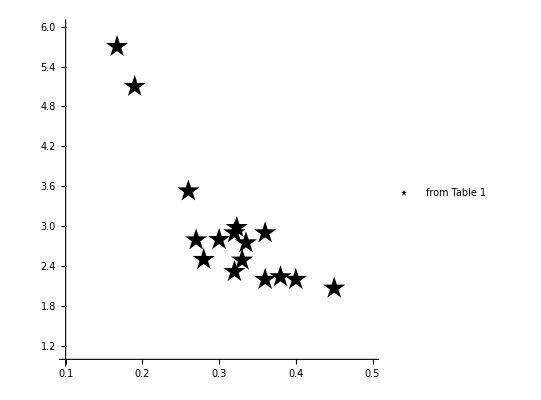

```mathematica
outline=ListPlot[pts2[[All,{1,2}]],PlotRange-> {{0.1,0.5},{1,6}},AspectRatio->1,PlotMarkers->{"★",24},PlotStyle->{{Black}},PlotLegends->{Style["from Table 1",18]},LabelStyle->(FontFamily->"Times")]
```

```mathematica
outline=ListPlot[pts2[[All,{1,2}]],PlotRange-> {{0.1,0.5},{1,6}},AspectRatio->1,PlotMarkers->{"★",24},PlotStyle->{{Black}},PlotLegends->{Style["from Table 1",18,Bold]},LabelStyle->(FontFamily->"Times")];
```

```mathematica
Show[outline,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfun[9],Pltfun[10],Pltfun[11],Pltfun[12],Pltfun[13],Pltfun[14],Pltfun[15],Pltfun[16],Pltfun[17],Pltfun[18]];
```

```mathematica
Show[ListPlot[pts2[[All,{1,2}]],PlotRange-> {{0.9,1.2},{0.5,6}},AspectRatio->1,PlotMarkers->{"★",24},PlotStyle->{{Black}},PlotLegends->{Style["from Table 1",18]},LabelStyle->(FontFamily->"Times")],Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfun[9],Pltfun[10],Pltfun[11],Pltfun[12],Pltfun[13],Pltfun[14],Pltfun[15],Pltfun[16],Pltfun[17],Pltfun[18]];
```

```mathematica
Regg[m_]:=0.0114 ((m/1.44)^(-2/3)-(m/1.44)^(2/3))^(1/2)(1+3.5(m/(5.7 10^-4))^(-2/3)+((5.7 10^-4)/m))^(-2/3)
```

```mathematica
plotegg =Plot[100Regg[m],{m,0.15,0.5},AspectRatio->1,AxesLabel-> {Style["mass (solar)",16],Style["radius (solar)",16]},BaseStyle->{FontSize->15},LabelStyle->(FontFamily->"Times"),PlotStyle->{Black,Thick},PlotRange-> {{0.15,0.5},{100 0.013,100 0.06}},PlotLegends->{Style["R(m)",16,Italic]},FrameLabel-> {Style["m_i (M_⊙)",16],Style["R_i (R_⊙)",16],Style["White dwarf masses and radii",Bold,16], Style["R_i (10^8cm)",16]},BaseStyle->{FontSize->15},LabelStyle->(FontFamily->"Times"),Frame-> True,FrameTicks->{{{.1,.2,.3,.4,.5},{Automatic},ChartingScaledTicks[{#/(Rsol/10^8)&,Rsol/10^8#&}]}}];
```

```mathematica
Plot[100Regg[m],{m,0.15,0.5},AspectRatio->1,AxesLabel-> {Style["mass (solar)",16],Style["radius (solar)",16]},BaseStyle->{FontSize->15},LabelStyle->(FontFamily->"Times"),PlotStyle->{Black,Thick},PlotRange-> {{0.15,0.5},{100 0.013,100 0.06}},PlotLegends->{Style[" \"cold\" ",16]},FrameLabel-> {Style["m_i (M_⊙)",16],Style["R_i (R_⊙)",16],Style["White dwarf masses and radii",Bold,16], Style["R_i (10^8cm)",16]},BaseStyle->{FontSize->15},LabelStyle->(FontFamily->"Times"),Frame-> True,FrameTicks->{{{.1,.2,.3,.4,.5},{Automatic},ChartingScaledTicks[{#/(Rsol/10^8)&,Rsol/10^8#&}]}}];
```

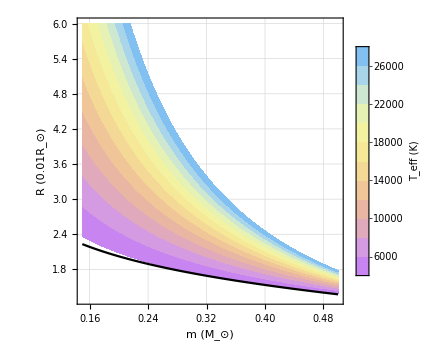

```mathematica
Show[contourprim,plotegg]
```

```mathematica
Show[outline,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfun[9],Pltfun[10],Pltfun[11],Pltfun[12],Pltfun[13],Pltfun[14],Pltfun[15],Pltfun[16],Pltfun[17],Pltfun[18]];
```

```mathematica
contourprimempty= ContourPlot[0(1.1798232975286564*^47 Log[mmm]^2-1.4023785637137418*^48 Log[mmm] Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]+4.167288525500679*^48 Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]^2)/(7.70388920852663*^43+3.4482434674930335*^44 Log[mmm]+3.858565034251842*^44 Log[mmm]^2) ,{mmm,0.15,0.5},{rr,1.3,6},Contours-> {1,4000,6000,8000,10000,12000,14000,16000,18000,20000,22000,24000,26000,28000},ImageSize-> Medium,ColorFunction->"Pastel", Axes-> True,FrameLabel->{Style["m (M_⊙)",Bold,20],Style["R (0.01R_⊙)",Bold,20]},FrameTicksStyle->Directive[FontSize->20],ContourStyle->None,ScalingFunctions->{None,None},BaseStyle->{FontSize->20},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["T_eff (K)",Bold],LabelStyle->labels],{After,Top}],PlotRange->{{0.15,0.5},{1.3,6},{4000,28000}},LabelStyle->(FontFamily->"Times")
];
```

```mathematica
Show[contourprimempty,plotegg,outline,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfun[9],Pltfun[10],Pltfun[11],Pltfun[12],Pltfun[13],Pltfun[14],Pltfun[15],Pltfun[16],Pltfun[17],Pltfun[18]];
```

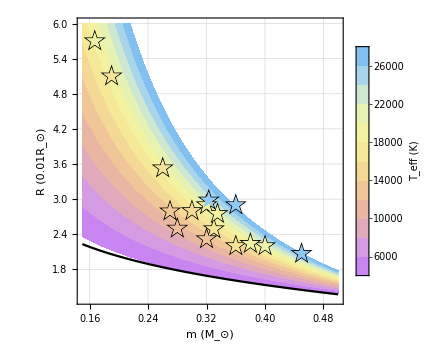

```mathematica
Show[contourprim,plotegg,outline,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfun[9],Pltfun[10],Pltfun[11],Pltfun[12],Pltfun[13],Pltfun[14],Pltfun[15],Pltfun[16],Pltfun[17],Pltfun[18]]
```

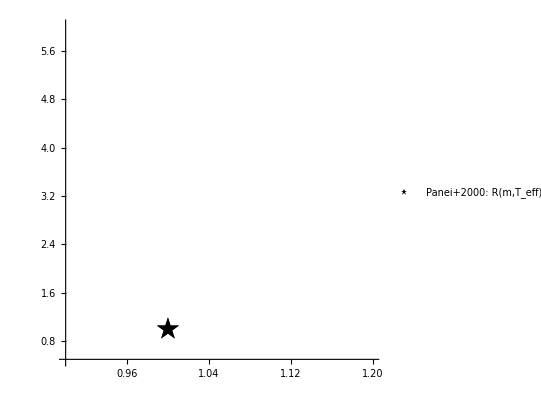

```mathematica
Show[ListPlot[pts2[[All,{1,2}]],PlotRange-> {{0.9,1.2},{0.5,6}},AspectRatio->1,PlotMarkers->{"★",24},PlotStyle->{{Black}},PlotLegends->{Style["Panei+2000: R(m,T_eff) ∝ m^(T_eff^(1/2))",18]},LabelStyle->(FontFamily->"Times")]]
```

## Figure 2 : tidal heating vs cooling regime

```mathematica
fdotTD1[m1_,m2_,fGW_,R1_]=(18 fGW^(13/3)  m2  π^(13/3) R1^5 (fGW/2))/(G^(5/3)m1 (m1+m2)^(5/3))konQ1
```

(1.17044×10^15 fGW^(16/3) konQ1 m2 R1^5)/(m1 (m1+m2)^(5/3))

```mathematica
fdotGW[m1_,m2_,fGW_] = (96 π^(8/3)G^(5/3)(fGW)^(11/3)(Mchirpf[m1,m2])^(5/3))/(5 c^5)//FullSimplify
```

1.83501×10^-62 fGW^(11/3) ((m1 m2)^(3/5)/(m1+m2)^(1/5))^(5/3)

```mathematica
ratiosol = konQ1/.Solve[fdotTD1[0.21 Msol,0.61 Msol,0.0048,0.0314Rsol] ==0.1 fdotGW[0.21 Msol,0.61 Msol,0.0048] ,konQ1][[1]]
```

7.6605×10^-12

```mathematica
RPanei[m_,T_]:=0.0132 10^(-0.00177 T^(1/2))m^(0.148-0.00941 T^(1/2))
```

```mathematica
Rscale[m1a_,T1a_]:=10^(-0.02792426461145596+0.7641778013995925 √T1a) m1a^(0.14797691065884058-0.9408955042478873 √T1a)
```

```mathematica
kQratio =8 10^-12;
```

```mathematica
WDid = {J0538,J0533,J2029,J0722,J1749,J1901,J2243,J0651,J1539};
m1prims={0.32,0.167,0.32,0.33,0.28,0.36,0.323,0.26,0.21};
T1prims={12.8,20,18.25,16.8,12,26,26.3,16.53,10} 1000;
m2secs={0.45,0.652,0.3,0.38,0.4,0.36,0.335,0.5,0.61};
Porb = {866.6,1233.97,1252.06,1422.55,1586.03,2436.11,528,765,414.8};
fGWs = 2/Porb
```

{0.00230787,0.00162078,0.00159737,0.00140593,0.00126101,0.000820981,1/264,2/765,0.0048216}

```mathematica
Rscale[m1prims 10,T1prims/10000]
```

{2.36408,6.1573,2.73582,2.55237,2.59701,2.77078,3.23396,3.26576,3.02524}

```mathematica
fGWRL=2^(3/2)/(9 π)((G m1prims Msol)/(Rscale[m1prims 10,T1prims/10000]Rsol/100)^3)^(1/2)
```

{0.00971922,0.0016704,0.00780715,0.00879815,0.00789618,0.00812451,0.00610308,0.00539583,0.005439}

```mathematica
Rscale[m1prims 10,T1prims/10000]
```

{2.36408,6.1573,2.73582,2.55237,2.59701,2.77078,3.23396,3.26576,3.02524}

```mathematica
RPanei
```

RPanei

```mathematica
RPanei[m1prims,T1prims]
```

{0.0236543,0.0616041,0.0273707,0.025536,0.0259858,0.0277161,0.0323496,0.0326745,0.0302729}

```mathematica
Rscale[m1prims 10,T1prims/10000]
```

{2.36408,6.1573,2.73582,2.55237,2.59701,2.77078,3.23396,3.26576,3.02524}

```mathematica
testZ = 0.02;
Atest=4;
Lsol=3.826 10^33;
Tcold = 4000;
```

```mathematica
L2a[m1_,t_,Z_]:=(300 m1 Z^0.4)/(Atest(t+0.1))^1.18;
```

```mathematica
L2b[m1_,t_,Z_]:=(300(9000 Atest)^5.3 m1 Z^0.4)/(Atest(t+0.1))^6.48;
```

```mathematica
τcools2=(t/.Table[NSolve[7.1 10^-4(Rsol RPanei[m1prims[[i]],Tcold])^2 Tcold^4==Piecewise[{{L2a[m1prims[[i]],t,testZ],t<9000},{L2b[m1prims[[i]],t,testZ],t>9000}}]Lsol,t],{i,1,9}])//Flatten
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

{9325.86,3851.99,9325.86,9410.13,8830.64,9652.56,9351.34,7840.16,5564.45}

```mathematica
RPanei[m1prims[[2]],T1prims[[2]]]
```

0.0616041

```mathematica
fGWs
```

{0.00230787,0.00162078,0.00159737,0.00140593,0.00126101,0.000820981,1/264,2/765,0.0048216}

```mathematica
τmergeTDfixMyr2 =Table[(2/3 2/18 (( G^(5/3) m1prims[[i]] (m1prims[[i]]Msol+m2secs[[i]] Msol)^(5/3) kQratio^-1)/(fGWs[[i]]^(13/3)  m2secs[[i]] π^(13/3) (Rsol/100 Rscale[m1prims[[i]] 10,T1prims[[i]]/10000])^5)))/(3.15 10^7 10^6),{i,1,9}]
```

{711.981,10.9677,1766.42,4434.85,4887.26,35675.7,18.1169,58.9895,4.58024}

```mathematica
τmergers=Table[Integrate[((96 π^(8/3) G^(5/3))/(5 c^5)(Mchirpf[m1prims[[i]]  Msol,m2secs[[i]]  Msol])^(5/3)f^(11/3))^-1,{f,fGWs[[i]],100}], {i,1,9}]/(3.146 10^7 10^6)
```

{1.40009,4.85044,5.21232,5.86778,8.6554,23.9443,0.471726,1.10729,0.225319}

```mathematica
τRL = Table[Integrate[((96 π^(8/3) G^(5/3))/(5 c^5)(Mchirpf[m1prims[[i]]  Msol,m2secs[[i]]  Msol])^(5/3)f^(11/3))^-1,{f,fGWs[[i]],fGWRL[[i]]}], {i,1,9}]/(3.146 10^7 10^3)
```

{1369.82,374.761,5136.56,5823.65,8590.42,23891.3,339.511,946.937,61.9168}

```mathematica
Table[Integrate[((96 π^(8/3) G^(5/3))/(5 c^5)(Mchirpf[m1prims[[i]]  Msol,m2secs[[i]]  Msol])^(5/3)f^(11/3))^-1,{f,fGWs[[i]],fGWRL[[i]]}], {i,1,9}]/(3.146 10^7 10^6)
```

{1.36982,0.374761,5.13656,5.82365,8.59042,23.8913,0.339511,0.946937,0.0619168}

```mathematica
Table[Integrate[((96 π^(8/3) G^(5/3))/(5 c^5)(Mchirpf[m1prims[[i]]  Msol,m2secs[[i]]  Msol])^(5/3)f^(11/3))^-1,{f,fGWs[[i]],100}], {i,1,9}]/(3.146 10^7 10^6)
```

{1.40009,4.85044,5.21232,5.86778,8.6554,23.9443,0.471726,1.10729,0.225319}

```mathematica
df1 = Transpose[{-Log10[τmergeTDfixMyr2/τcools2],T1prims,-Log[τRL]}]
```

{{1.11722,12800.,-7.22243},{2.54557,20000,-5.92629},{0.722596,18250.,-8.54414},{0.326716,16800.,-8.66968},{0.256927,12000,-9.0584},{-0.56773,26000,-10.0813},{2.71279,26300.,-5.82751},{2.12355,16530.,-6.85323},{3.08453,10000,-4.12579}}

{{1.11722,12800.,-7.22243},{2.54557,20000,-5.92629},{0.722596,18250.,-8.54414},{0.326716,16800.,-8.66968},{0.256927,12000,-9.0584},{-0.56773,26000,-10.0813},{2.71279,26300.,-5.82751},{2.12355,16530.,-6.85323},{3.08453,10000,-4.12579}}

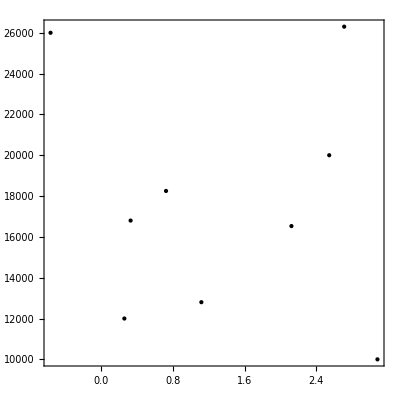

```mathematica
pts2=df1
Graphics[{AbsoluteThickness[3],Point[pts2[[All,{1,2}]],VertexColors->ColorData["Pastel"]/@Rescale[pts2[[All,3]]]]},AspectRatio->1,Frame->True]
```

```mathematica
stylesTemp=ColorData["CMYKColors"]/@Rescale[pts2[[All,3]]]
```

{RGBColor[0.9006669394031216, 0.5961144135876842, 0.5311602164226983],RGBColor[0.9167911155882699, 0.8494176649479984, 0.5102866363400644],RGBColor[0.6870336674559032, 0.44314597351216056, 0.7161360755444905],RGBColor[0.6570236253716583, 0.4701985216169528, 0.7393903324399183],RGBColor[0.5585970906116938, 0.5719815465422209, 0.8161661331212269],RGBColor[0.300725, 0.680491, 0.901701],RGBColor[0.9061904809884459, 0.8497266749269451, 0.5191170567690304],RGBColor[0.9310368305269642, 0.7022019596443408, 0.49782748619437683],RGBColor[0.133532, 0.122103, 0.125444]}

```mathematica
stylesTemp=ColorData["AvocadoColors"]/@Rescale[pts2[[All,3]]]
```

{RGBColor[0.2662200001907112, 0.6657607184981627, 0.10605701492452253],RGBColor[0.6013843137674506, 0.8003817268070299, 0.1380590176732216],RGBColor[0.00937829904775014, 0.45071129874853755, 0.07602228589411995],RGBColor[0., 0.41987114073143866, 0.07103637307131046],RGBColor[0., 0.3042478657503067, 0.05147451872957574],RGBColor[0., 0., 0.],RGBColor[0.6275689203849568, 0.8100543528554804, 0.14051756276819707],RGBColor[0.3556737798620434, 0.7096159518863118, 0.11498857645020658],RGBColor[1., 0.984375, 0.230411]}

```mathematica
Pltfun[ii_]:=ListPlot[{pts2[[All,{1,2}]][[ii]]},PlotRange-> {{-1.5,4.2},{6000,32000}},AspectRatio->1,PlotMarkers->{"★",18},PlotStyle->{{stylesTemp[[ii]]}},LabelStyle->(FontFamily->"Times")]
```

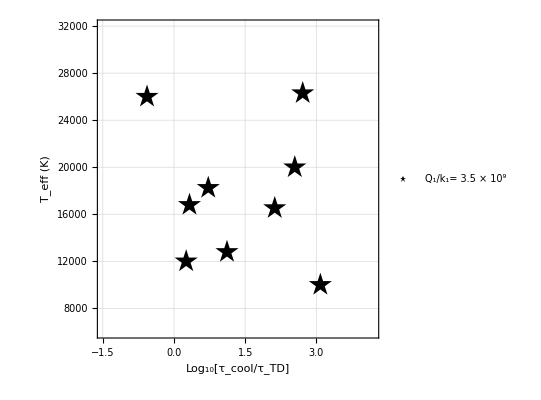

```mathematica
br2=ListPlot[Transpose[{-Log10[τmergeTDfixMyr2/τcools2],T1prims}],AspectRatio->1,PlotMarkers->{"★",25},PlotStyle->{{Black},"*"},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},PlotRange->{{-1.5,4.2},{6000,32000}},PlotLegends->{Style["Q_1/k_1= 3.5 × 10^9",16]},GridLines->Automatic]
```

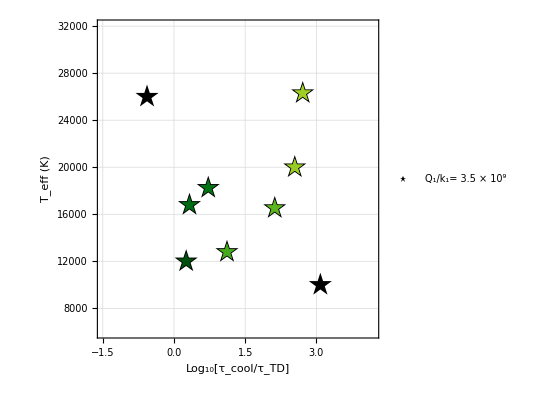

```mathematica
Show[br2,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8]]
```

```mathematica
WDid
```

{J0538,J0533,J2029,J0722,J1749,J1901,J2243,J0651,J1539}

```mathematica
(τmergeTDfixMyr2/τcools2)^-1
```

{13.0985,351.211,5.27954,2.12186,1.80687,0.270564,516.166,132.908,1214.88}

```mathematica
Log10[Min[τRL]]
```

1.79181

```mathematica
Log10[Max[τRL]]
```

4.37824

```mathematica
τRL
```

{1369.82,374.761,5136.56,5823.65,8590.42,23891.3,339.511,946.937,61.9168}

```mathematica
labels=Directive[FontSize->18,FontFamily->"Times"];
```

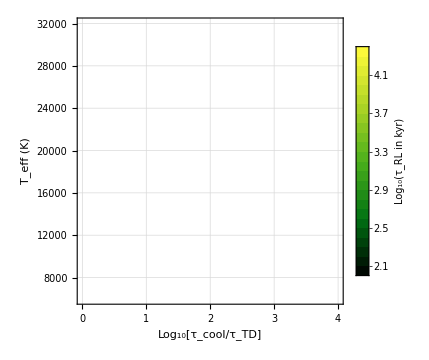

```mathematica
cptrack =ContourPlot[ tscale,{ratio,0,4},{tscale,Min[Log10[τRL]],Max[Log10[τRL]]},Contours-> Table[(i+1)0.1,{i,0,43}],ImageSize-> Medium,ColorFunction->(ColorData["AvocadoColors"]), Axes-> True,FrameTicksStyle->Directive[FontSize->18],ContourStyle->None,ScalingFunctions->{None,None,None},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log_10(τ_RL in kyr)",18],LabelStyle->labels],{After,Top}],PlotRange->{{0,4},{6000,32000},{2,4.5}},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]",18],Style["T_eff (K)",18]},GridLines->Automatic,FrameStyle->Automatic]
```

```mathematica
cptrack =ContourPlot[ tscale,{ratio,0,4},{tscale,2,5},Contours-> Table[(i+1)0.1,{i,0,43}],ImageSize-> Medium,ColorFunction->(ColorData["AvocadoColors"]), Axes-> True,FrameTicksStyle->Directive[FontSize->18],ContourStyle->None,ScalingFunctions->{None,None,None},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log_10(τ_RL in kyr)",18],LabelStyle->labels],{After,Top}],PlotRange->{{0,4},{6000,32000},{2.5,4.5}},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]",18],Style["T_eff (K)",18]},GridLines->Automatic,FrameStyle->Automatic];
```

```mathematica
cptrack =ContourPlot[ tscale,{ratio,0,4},{tscale,2.5,4.5},Contours-> Table[(i+1)0.1,{i,0,43}],ImageSize-> Medium,ColorFunction->(ColorData["AvocadoColors"]), Axes-> True,FrameTicksStyle->Directive[FontSize->18,Black],ContourStyle->None,ScalingFunctions->{None,None,None},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log_10(τ_RL in kyr)",18],LabelStyle->labels],{After,Top}],PlotRange->{{0-1,3.3},{6000,32000},{2.5,4.5}},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]",18,Black],Style["T_eff (K)",18,Black]},GridLines->Automatic,FrameStyle->Automatic];
```

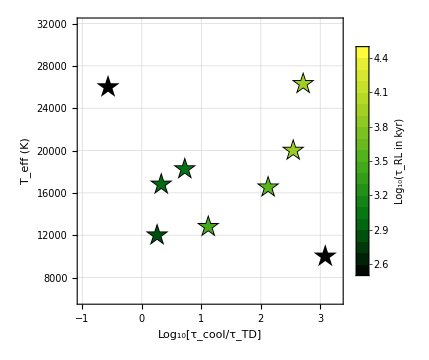

```mathematica
Show[cptrack,br2,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8]]
```

```mathematica
fGWs
```

{0.00230787,0.00162078,0.00159737,0.00140593,0.00126101,0.000820981,1/264,2/765,0.0048216}

```mathematica
τfricTD =Table[(1/9 (( G^(5/3) m1prims[[i]] (m1prims[[i]]Msol+m2secs[[i]] Msol)^(5/3) kQratio^-1)/(fGWs[[i]]^(13/3)  m2secs[[i]] π^(13/3) (Rsol/100 Rscale[m1prims[[i]] 10,T1prims[[i]]/10000])^5)))/(3.15 10^7 10^6),{i,1,9}]
```

{1067.97,16.4516,2649.62,6652.28,7330.89,53513.5,27.1754,88.4843,6.87036}

```mathematica
τTempTD =Table[(1/9 (( G^(5/3) m1prims[[i]] (m1prims[[i]]Msol+m2secs[[i]] Msol)^(5/3) kQratio^-1)/(fGWs[[i]]^(13/3)  m2secs[[i]] π^(13/3) (Rsol/100 Rscale[m1prims[[i]] 10,T1prims[[i]]/10000])^5)))/(3.15 10^7 10^6),{i,1,9}]
```

{1067.97,16.4516,2649.62,6652.28,7330.89,53513.5,27.1754,88.4843,6.87036}

```mathematica
τmergeTDfixMyr2
```

{711.981,10.9677,1766.42,4434.85,4887.26,35675.7,18.1169,58.9895,4.58024}

```mathematica
(1/9 (( G^(5/3) 0.21 Msol(0.21Msol+0.61 Msol)^(5/3) kQratio^-1)/((0.0048)^(13/3)  (0.61 Msol) π^(13/3) (Rsol/100 Rscale[0.21 10,10000/10000])^5)))/(3.15 10^7 10^6)
```

7.00535

```mathematica
τcool4
```

τcool4

```mathematica
τcools2
```

{9325.86,3851.99,9325.86,9410.13,8830.64,9652.56,9351.34,7840.16,5564.45}

```mathematica
T1prims
```

{12800.,20000,18250.,16800.,12000,26000,26300.,16530.,10000}

```mathematica
Tcold
```

4000

```mathematica
τcools3=(t/.Table[NSolve[7.1 10^-4(Rsol RPanei[m1prims[[i]],T1prims[[i]]/2.71])^2(T1prims[[i]]/2.71)^4==Piecewise[{{L2a[m1prims[[i]],t,testZ],t<9000},{L2b[m1prims[[i]],t,testZ],t>9000}}]Lsol,t],{i,1,9}])//Flatten
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

{5855.89,295.732,1513.94,2203.07,5986.,491.701,371.863,1510.42,7650.54}

```mathematica
τcools3/τfricTD
```

{5.48319,17.9759,0.571379,0.331175,0.816544,0.00918836,13.6838,17.0699,1113.56}

```mathematica
Log10[τcools2/τfricTD]
```

{0.941129,2.36948,0.546505,0.150625,0.0808355,-0.743821,2.5367,1.94746,2.90844}

```mathematica
br3=ListPlot[Transpose[{-Log10[τfricTD/τcools3],T1prims}],AspectRatio->1,PlotMarkers->{"★",25},PlotStyle->{{Black},"*"},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},PlotRange->{{-0.6,2},{6000,32000}},PlotLegends->{Style["Q_1/k_1= 3.5 × 10^9",16]},GridLines->Automatic];
```

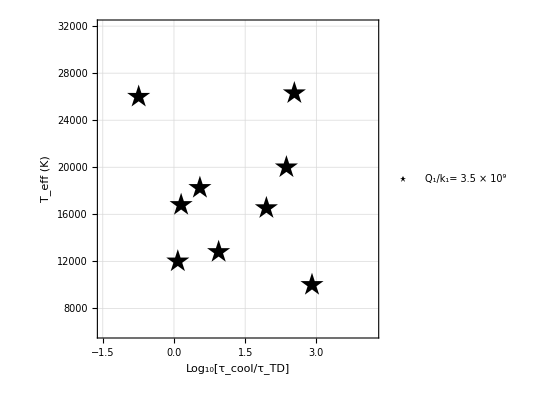

```mathematica
br4=ListPlot[Transpose[{-Log10[τfricTD/τcools2],T1prims}],AspectRatio->1,PlotMarkers->{"★",25},PlotStyle->{{Black},"*"},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},PlotRange->{{-1.5,4.2},{6000,32000}},PlotLegends->{Style["Q_1/k_1= 3.5 × 10^9",16]},GridLines->Automatic]
```

```mathematica
τcools2
```

{9325.86,3851.99,9325.86,9410.13,8830.64,9652.56,9351.34,7840.16,5564.45}

```mathematica
list1grey =  Transpose[{{-2,0},{0,0}}];
list2grey =  Transpose[{{-2,0},{400000,400000}}];
```

```mathematica
plotgrey=ListPlot[{list2grey,list1grey},Mesh->All,PlotMarkers->None,Joined->True,Filling->{1->{2}},FillingStyle->{Blend[{Gray,Gray,Black}],Opacity[.3]},PlotStyle-> {{Blend[{Gray,Gray,Black}],Opacity[0.5]}},PlotRange->{{-2,4},{0,222000}},AspectRatio->1,Frame->True,LabelStyle->(FontFamily->"Times"),GridLines->Automatic,PlotLegends->{Style["J0651 primary (Ω_0=0)",16]}];
```

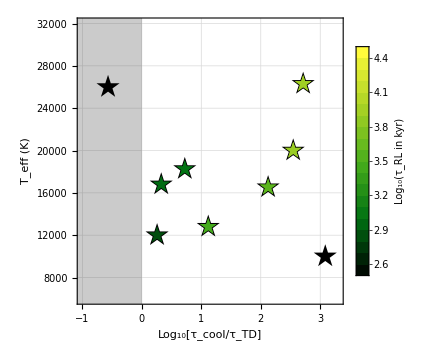

```mathematica
Show[cptrack,plotgrey,br2,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8]]
```

```mathematica
Correlation[-Log10[τmergeTDfixMyr2/τcools2],T1prims]
```

-0.130405

```mathematica
-Log10[τmergeTDfixMyr2/τcools2]
```

{1.11722,2.54557,0.722596,0.326716,0.256927,-0.56773,2.71279,2.12355,3.08453}

```mathematica
T1prims
```

{12800.,20000,18250.,16800.,12000,26000,26300.,16530.,10000}

```mathematica
Correlation[{1.1055364280752897,2.5373372402967753,0.7109120374281895,0.3150321837678671,0.24869520222317304,2.70110493365627,2.1153183985579185},{12800.,20000,18250.,16800.,12000,26300.,16530.}]
```

0.716418

```mathematica
J1539τ=(2/3 2/18 (( G^(5/3) 0.21 (0.21Msol+0.61 Msol)^(5/3) kQratio^-1)/(0.0048^(13/3)  0.61 π^(13/3) (Rsol/100 Rscale[0.21 10,10000/10000])^5)))/(3.15 10^7 10^6)
```

4.67023

```mathematica
τmergeTDfixMyr2
```

{711.981,10.9677,1766.42,4434.85,4887.26,35675.7,18.1169,58.9895,4.58024}

```mathematica
J1539τcool = (t/.NSolve[7.1 10^-4(Rsol RPanei[0.21,Tcold])^2 Tcold^4==Piecewise[{{L2a[0.21,t,testZ],t<9000},{L2b[0.21,t,testZ],t>9000}}]Lsol,t])//Flatten
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{5564.45}

```mathematica
J1539τratio=-Log10[J1539τ/J1539τcool ][[1]]
```

3.07608

```mathematica
J1539temp=10000
```

10000

```mathematica
(J1539τ/J1539τcool)^-1
```

{1191.47}

```mathematica
mtps=ResourceFunction["PolygonMarker"]["Triangle",{Offset[10],π},{EdgeForm[Blend[{Cyan,Blue,Cyan}]],FaceForm[stylesTemp[[9]]]}]
```

-Graphics-

```mathematica
stylesTemp[[8]]
```

RGBColor[0.3556737798620434, 0.7096159518863118, 0.11498857645020658]

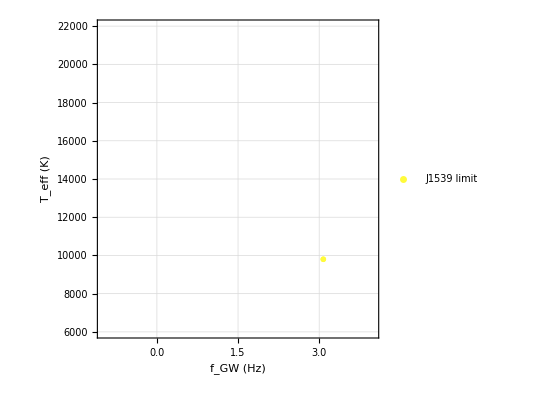

```mathematica
J1539plot = ListPlot[{Transpose[{J1539τratio,0.98J1539temp}]},PlotMarkers->{mtps},Joined->False,PlotStyle->{{stylesTemp[[9]]}},PlotRange->{{-1,4},{6000,22000}},AspectRatio->1,Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["f_GW (Hz)"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},GridLines->Automatic,PlotLegends->{Style["J1539 limit",16]}]
```

```mathematica
J1539τratio
```

3.07608

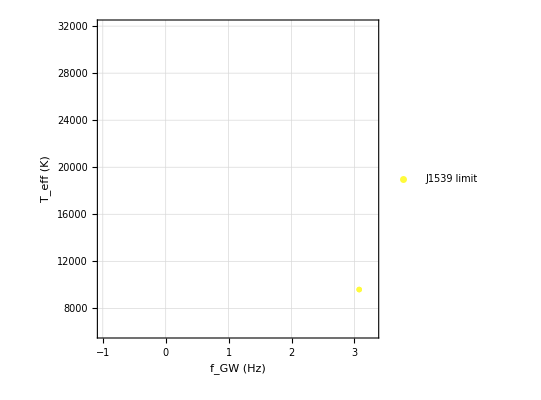

```mathematica
J1539plot = ListPlot[{Transpose[{J1539τratio,0.96J1539temp}]},PlotMarkers->{mtps},Joined->False,PlotStyle->{{stylesTemp[[9]]}},PlotRange->{{-1,3.3},{6000,32000}},AspectRatio->1,Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["f_GW (Hz)"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},GridLines->Automatic,PlotLegends->{Style["J1539 limit",16]}]
```

```mathematica
Pltfunwhite[ii_]:=ListPlot[{pts2[[All,{1,2}]][[ii]]},PlotRange-> {{-1.5,4.2},{6000,32000}},AspectRatio->1,PlotMarkers->{"★",40},PlotStyle->{White},LabelStyle->(FontFamily->"Times")]
```

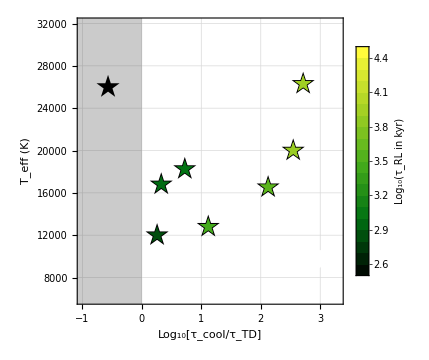

```mathematica
Show[cptrack,plotgrey,br2,J1539plot,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfunwhite[9],J1539plot]
```

## Figure 3 : tracks for three binaries

### Relations

```mathematica
Rscale[m1a_,T1a_]:=10^(-0.02792426461145596+0.7641778013995925 √T1a) m1a^(0.14797691065884058-0.9408955042478873 √T1a)
```

```mathematica
dRscaledt[m1a_,T1a_]:=1/(√T1a)0.8797922069498331 10^(-0.02792426461145596+0.7641778013995925 √T1a) m1a^(0.14797691065884058-0.9408955042478873 √T1a)-1/(√T1a)0.47044775212394363 10^(-0.02792426461145596+0.7641778013995925 √T1a) m1a^(0.14797691065884058-0.9408955042478873 √T1a) Log[m1a]
```

```mathematica
Mchirpf[m11_,m22_]=(m11 m22)^(3/5)/(m11+m22)^(1/5);
```

### J2029

```mathematica
mp=3.2;
ms=3.0;
fbin=1.6;
Tp=1.825;
```

```mathematica
kQratioa =   8 10^-12;
```

```mathematica
preGW=D[fGW/mHz,fGW](96 G^(5/3)π^(8/3)(Msol/10)^(5/3))/(5 c^5)(mHz)^(11/3)D[t/(31.46 10^13),t]^-1
preTDa=D[fGW/mHz,fGW](18 (mHz)^(13/3) (Msol/10)  π^(13/3) (Rsol/100)^5 (mHz))/(G^(5/3) (Msol/10)((Msol/10))^(5/3))kQratioa D[t/(31.46 10^13),t]^-1
```

0.0394863

0.00014425

```mathematica
preΩa=  D[Ω/mHz,Ω]((3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^3 (mHz))/(G  (Msol/10)rg2((Msol/10))^2))kQratioa D[t/(31.46 10^13),t]^-1
```

0.0600658

```mathematica
dΩdf=((preGW (mp ms) (1/(mp +ms)^(1/3)) fbin^(11/3))+ms/(mp(mp+ms)^(5/3))preTDa fbin^(13/3) (Rscale[mp,Tp])^5(fbin/2-Ω)1/(1-2 Ω/fbin)  )^-1(preΩa 1/(1-2 Ω/fbin)ms^2/(mp(mp+ms)^2) fbin^3 (Rscale[mp,Tp])^3(fbin/2-Ω))
d2Ωdf2[f_]=D[((preGW (mp ms) (1/(mp +ms)^(1/3)) f^(11/3))+ms/(mp(mp+ms)^(5/3))preTDa 1/(1-2 Ω/f) f^(13/3) (Rscale[mp,Tp])^5(f/2-Ω))^-1(preΩa 1/(1-2 Ω/f)ms^2/(mp(mp+ms)^2) f^3 (Rscale[mp,Tp])^3(f/2-Ω)),f]
Ωstart=Ω/.FindRoot[(2 Ω)/fbin^3-(2 dΩdf)/fbin^2+d2Ωdf2[fbin]/fbin==0,{Ω,0.9}][[1]]
factorsyn = 2 Ωstart/fbin
kQratiob = 1/(1-factorsyn)  8 10^-12;
```

(0.368603 (0.8-Ω))/((1.15618+(0.00759264 (0.8-Ω))/(1-1.25 Ω)) (1-1.25 Ω))

-((0.089991 f^3 (f/2-Ω) (0.756586 f^(8/3)-(0.00198108 f^(7/3) (f/2-Ω) Ω)/(1-(2 Ω)/f)^2+(0.000495271 f^(13/3))/(1-(2 Ω)/f)+(0.00429235 f^(10/3) (f/2-Ω))/(1-(2 Ω)/f)))/((1-(2 Ω)/f) (0.206342 f^(11/3)+(0.000990542 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f))^2))-(0.179982 f (f/2-Ω) Ω)/((1-(2 Ω)/f)^2 (0.206342 f^(11/3)+(0.000990542 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))+(0.0449955 f^3)/((1-(2 Ω)/f) (0.206342 f^(11/3)+(0.000990542 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))+(0.269973 f^2 (f/2-Ω))/((1-(2 Ω)/f) (0.206342 f^(11/3)+(0.000990542 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))

0.340055

0.425069

```mathematica
preTDb=D[fGW/mHz,fGW](18 (mHz)^(13/3) (Msol/10)  π^(13/3) (Rsol/100)^5 (mHz))/(G^(5/3) (Msol/10)((Msol/10))^(5/3))kQratiob D[t/(31.46 10^13),t]^-1
```

0.0002509

```mathematica
preTb=D[T/kK4,T]((135 mHz^(19/3)  (Msol/10)^3 π^(25/3)  (Rsol/100)^9)/(G^(8/3) (Msol/10) σ ((Msol/10))^(11/3)  kK4^3 ((Rsol/100)))(mHz)^3)kQratiob^2 D[t/(31.46 10^13),t]^-1
```

0.0000230828

```mathematica
preJb=D[J/((Msol/10)(Rsol/100)^2 mHz),J](2 π(3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^5 (mHz))/(G ((Msol/10))^2))kQratiob D[t/(31.46 10^13),t]^-1
```

0.0656433

```mathematica
preΩb=D[Ω/mHz,Ω]((3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^3 (mHz))/(G  (Msol/10)rg2((Msol/10))^2))kQratiob D[t/(31.46 10^13),t]^-1
```

0.104475

```mathematica
soltestgenb=NDSolve[{f'[t]==(preGW (mp ms) (1/(mp +ms)^(1/3)) f[t]^(11/3))+ms/(mp(mp+ms)^(5/3))preTDb f[t]^(13/3) (Rscale[mp,T[t]])^5(f[t]/2-Ω[t]),
T'[t]==preTb(((ms)^3 f[t]^(19/3)Rscale[mp,T[t]]^9 (f[t]/2-Ω[t])^2(f[t]/2-3/5 Ω[t]))/((mp(mp+ms)^(11/3))(T[t]^3(2 Rscale[mp,T[t]]+T[t]dRscaledt[mp,T[t]])))),
Ω'[t]==preΩb ms^2/(mp(mp+ms)^2) f[t]^3 (Rscale[mp,T[t]])^3(f[t]/2-Ω[t]),
f[0]==fbin,T[0]==Tp,Ω[0]== factorsyn fbin/2  },{f,T,Ω},{t,0,0.51},Method->"StiffnessSwitching"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::nlnum: The function value {2.00672×10^20,Indeterminate,0.} is not a list of numbers with dimensions {3} at {t,f[t],T[t],Ω[t]} = {0.51,529630.,3.77064×10^7,3912.11}.

{{f→InterpolatingFunction[…],T→InterpolatingFunction[…],Ω→InterpolatingFunction[…]}}

```mathematica
endt=0.51;
stepsize=0.0001;
```

```mathematica
fvals1b=Table[Evaluate[f[t]/.soltestgenb],{t,0,endt,stepsize}]//Abs//Flatten;
Tvals1b=Table[Evaluate[T[t]/.soltestgenb],{t,0,endt,stepsize}]//Flatten;
Ωvals1b=Table[Evaluate[Ω[t]/.soltestgenb],{t,0,endt,stepsize}]//Flatten;
timevals1b = Table[t,{t,0,endt,stepsize}]//Flatten;
avals1b=(G^(1/3) (( mp+ms)Msol/10 )^(1/3))/((fvals1b mHz)^(2/3) π^(2/3))/(Rsol/100);
Rvals1b=Rscale[mp,Tvals1b];
Ra1b =Rvals1b/avals1b;

RRLval
RRLval =3^(-4/3)2 mp^(1/3)/(mp+ms)^(1/3);
RRLval=(0.49(mp/ms)^(2/3))/(0.6 (mp/ms)^(2/3)+Log[1+(mp/ms)^(1/3)])
Tvals2b =Pick[Tvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
fvals2b=Pick[fvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Ωvals2b=Pick[Ωvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
timevals2b=Pick[timevals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Ra1cutb=Pick[Ra1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Rvals2b=Pick[Rvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
```

InterpolatingFunction::dmval: Input value {0.5084} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5085} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5086} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.5084} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5085} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5086} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.5084} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5085} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5086} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

RRLval

0.38452

```mathematica
RLposia=x/.Solve[Position[Abs[Ra1cutb/RRLval-1],Min[Abs[Ra1cutb/RRLval-1]]]==x][[1]];
Abs[Ra1cutb/RRLval-1][[RLposia]];
fvals2b[[RLposia]]
Tvals2b[[RLposia]]kK4
```

7.24804

21727.6

```mathematica
Tvals2b//Length
```

5046

```mathematica
x4={{12012,"0.01"},{13897,"0.02"},{16049,"0.04"},{18502,"0.08"},{21291,"0.16"},{24454,"0.32"},{28031,"0.64 L_☉"}};
```

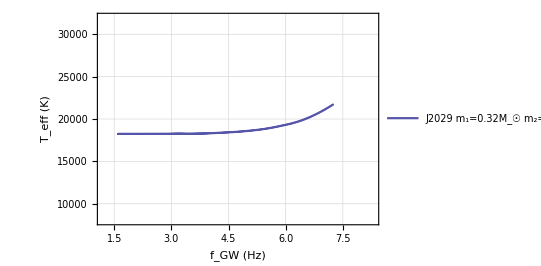

```mathematica
plota21lin=ListPlot[Transpose[{fvals2b[[;;RLposia]],10^4 Tvals2b[[;;RLposia]]}],Mesh->All,PlotMarkers->None,Joined-> True,PlotStyle-> Blend[{Gray,Gray,Blue}],PlotRange->{1000{0.0012,0.0083},{8000,32000}},AspectRatio->1/1.5,Frame->True,LabelStyle->{(FontFamily->"Times"),Black},FrameLabel-> {Style["f_GW (Hz)"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},GridLines->Automatic,PlotLegends->{Style["J2029 m_1=0.32M_☉ m_2=0.30M_☉ , Ω_0=0.42f_orb",16]},FrameTicks->{{Automatic,x4},{Automatic,Automatic}}]
```

### J2243

```mathematica
mp=3.23;
ms=3.35;
fbin=3.8;
Tp=2.63;
```

```mathematica
preGW=D[fGW/mHz,fGW](96 G^(5/3)π^(8/3)(Msol/10)^(5/3))/(5 c^5)(mHz)^(11/3)D[t/(31.46 10^13),t]^-1
preTDa=D[fGW/mHz,fGW](18 (mHz)^(13/3) (Msol/10)  π^(13/3) (Rsol/100)^5 (mHz))/(G^(5/3) (Msol/10)((Msol/10))^(5/3))kQratioa D[t/(31.46 10^13),t]^-1
```

0.0394863

0.00014425

```mathematica
preΩa=  D[Ω/mHz,Ω]((3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^3 (mHz))/(G  (Msol/10)rg2((Msol/10))^2))kQratioa D[t/(31.46 10^13),t]^-1
```

0.0600658

```mathematica
kQratioa =   8 10^-12;
```

```mathematica
dΩdf=((preGW (mp ms) (1/(mp +ms)^(1/3)) fbin^(11/3))+ms/(mp(mp+ms)^(5/3))preTDa fbin^(13/3) (Rscale[mp,Tp])^5(fbin/2-Ω)1/(1-2 Ω/fbin)  )^-1(preΩa 1/(1-2 Ω/fbin)ms^2/(mp(mp+ms)^2) fbin^3 (Rscale[mp,Tp])^3(fbin/2-Ω))
d2Ωdf2[f_]=D[((preGW (mp ms) (1/(mp +ms)^(1/3)) f^(11/3))+ms/(mp(mp+ms)^(5/3))preTDa 1/(1-2 Ω/f) f^(13/3) (Rscale[mp,Tp])^5(f/2-Ω))^-1(preΩa 1/(1-2 Ω/f)ms^2/(mp(mp+ms)^2) f^3 (Rscale[mp,Tp])^3(f/2-Ω)),f]
Ωstart=Ω/.FindRoot[(2 Ω)/fbin^3-(2 dΩdf)/fbin^2+d2Ωdf2[fbin]/fbin==0,{Ω,0.9}][[1]]
factorsyn = 2 Ωstart/fbin
kQratiob = 1/(1-factorsyn)  8 10^-12;
```

(8.94572 (1.9-Ω))/((30.4667+(0.745272 (1.9-Ω))/(1-0.526316 Ω)) (1-0.526316 Ω))

-((0.163029 f^3 (f/2-Ω) (0.836033 f^(8/3)-(0.00458088 f^(7/3) (f/2-Ω) Ω)/(1-(2 Ω)/f)^2+(0.00114522 f^(13/3))/(1-(2 Ω)/f)+(0.00992525 f^(10/3) (f/2-Ω))/(1-(2 Ω)/f)))/((1-(2 Ω)/f) (0.228009 f^(11/3)+(0.00229044 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f))^2))-(0.326058 f (f/2-Ω) Ω)/((1-(2 Ω)/f)^2 (0.228009 f^(11/3)+(0.00229044 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))+(0.0815145 f^3)/((1-(2 Ω)/f) (0.228009 f^(11/3)+(0.00229044 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))+(0.489087 f^2 (f/2-Ω))/((1-(2 Ω)/f) (0.228009 f^(11/3)+(0.00229044 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))

1.76315

0.927973

```mathematica
preTDb=D[fGW/mHz,fGW](18 (mHz)^(13/3) (Msol/10)  π^(13/3) (Rsol/100)^5 (mHz))/(G^(5/3) (Msol/10)((Msol/10))^(5/3))kQratiob D[t/(31.46 10^13),t]^-1
```

0.00200272

```mathematica
preTb=D[T/kK4,T]((135 mHz^(19/3)  (Msol/10)^3 π^(25/3)  (Rsol/100)^9)/(G^(8/3) (Msol/10) σ ((Msol/10))^(11/3)  kK4^3 ((Rsol/100)))(mHz)^3)kQratiob^2 D[t/(31.46 10^13),t]^-1
```

0.00147072

```mathematica
preJb=D[J/((Msol/10)(Rsol/100)^2 mHz),J](2 π(3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^5 (mHz))/(G ((Msol/10))^2))kQratiob D[t/(31.46 10^13),t]^-1
```

0.523975

```mathematica
preΩb=D[Ω/mHz,Ω]((3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^3 (mHz))/(G  (Msol/10)rg2((Msol/10))^2))kQratiob D[t/(31.46 10^13),t]^-1
```

0.833933

```mathematica
soltestgenb=NDSolve[{f'[t]==(preGW (mp ms) (1/(mp +ms)^(1/3)) f[t]^(11/3))+ms/(mp(mp+ms)^(5/3))preTDb f[t]^(13/3) (Rscale[mp,T[t]])^5(f[t]/2-Ω[t]),
T'[t]==preTb(((ms)^3 f[t]^(19/3)Rscale[mp,T[t]]^9 (f[t]/2-Ω[t])^2(f[t]/2-3/5 Ω[t]))/((mp(mp+ms)^(11/3))(T[t]^3(2 Rscale[mp,T[t]]+T[t]dRscaledt[mp,T[t]])))),
Ω'[t]==preΩb ms^2/(mp(mp+ms)^2) f[t]^3 (Rscale[mp,T[t]])^3(f[t]/2-Ω[t]),
f[0]==fbin,T[0]==Tp,Ω[0]== 0.9fbin/2  },{f,T,Ω},{t,0,0.05},Method->"StiffnessSwitching"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::nlnum: The function value {4.05494×10^55,Indeterminate,0.} is not a list of numbers with dimensions {3} at {t,f[t],T[t],Ω[t]} = {0.041261,2.19239×10^15,9.31949×10^21,5.33244×10^9}.

{{f→InterpolatingFunction[…],T→InterpolatingFunction[…],Ω→InterpolatingFunction[…]}}

```mathematica
endt=0.05;
stepsize=0.00001;
```

```mathematica
fvals1b=Table[Evaluate[f[t]/.soltestgenb],{t,0,endt,stepsize}]//Abs//Flatten;
Tvals1b=Table[Evaluate[T[t]/.soltestgenb],{t,0,endt,stepsize}]//Flatten;
Ωvals1b=Table[Evaluate[Ω[t]/.soltestgenb],{t,0,endt,stepsize}]//Flatten;
timevals1b = Table[t,{t,0,endt,stepsize}]//Flatten;
avals1b=(G^(1/3) (( mp+ms)Msol/10 )^(1/3))/((fvals1b mHz)^(2/3) π^(2/3))/(Rsol/100);
Rvals1b=Rscale[mp,Tvals1b];
Ra1b =Rvals1b/avals1b;

RRLval
RRLval =3^(-4/3)2 mp^(1/3)/(mp+ms)^(1/3);
RRLval=(0.49(mp/ms)^(2/3))/(0.6 (mp/ms)^(2/3)+Log[1+(mp/ms)^(1/3)])
Tvals2b =Pick[Tvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
fvals2b=Pick[fvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Ωvals2b=Pick[Ωvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
timevals2b=Pick[timevals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Ra1cutb=Pick[Ra1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Rvals2b=Pick[Rvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
```

InterpolatingFunction::dmval: Input value {0.0408} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04081} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0408} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04081} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0408} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04081} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.38452

0.375767

```mathematica
RLposia=x/.Solve[Position[Abs[Ra1cutb/RRLval-1],Min[Abs[Ra1cutb/RRLval-1]]]==x][[1]];
Abs[Ra1cutb/RRLval-1][[RLposia]];
fvals2b[[RLposia]]
Tvals2b[[RLposia]]kK4
```

6.20388

27251.6

```mathematica
Tvals2b//Length
```

3217

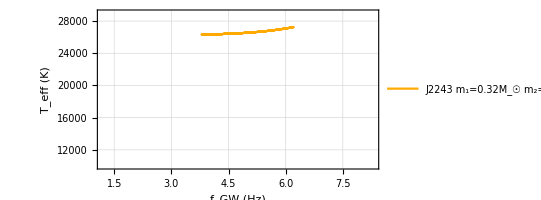

```mathematica
plota23lin=ListPlot[Transpose[{fvals2b[[;;RLposia]],10^4 Tvals2b[[;;RLposia]]}],Mesh->All,PlotMarkers->None,Joined-> True,PlotStyle->Blend[{Orange,Orange,Yellow}],PlotRange->{1000{0.0012,0.0083},{10000,29000}},AspectRatio->1/2,Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["f_GW (Hz)"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},GridLines->Automatic,PlotLegends->{Style["J2243 m_1=0.32M_☉ m_2=0.33M_☉ , Ω_0=0.91f_orb",16]}]
```

### J0538

```mathematica
mp=3.2;
ms=4.5;
fbin=2.3;
Tp=1.28;
```

```mathematica
preGW=D[fGW/mHz,fGW](96 G^(5/3)π^(8/3)(Msol/10)^(5/3))/(5 c^5)(mHz)^(11/3)D[t/(31.46 10^13),t]^-1
preTDa=D[fGW/mHz,fGW](18 (mHz)^(13/3) (Msol/10)  π^(13/3) (Rsol/100)^5 (mHz))/(G^(5/3) (Msol/10)((Msol/10))^(5/3))kQratioa D[t/(31.46 10^13),t]^-1
```

0.0394863

0.00014425

```mathematica
preΩa=  D[Ω/mHz,Ω]((3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^3 (mHz))/(G  (Msol/10)rg2((Msol/10))^2))kQratioa D[t/(31.46 10^13),t]^-1
```

0.0600658

```mathematica
kQratioa =   8 10^-12;
```

```mathematica
dΩdf=((preGW (mp ms) (1/(mp +ms)^(1/3)) fbin^(11/3))+ms/(mp(mp+ms)^(5/3))preTDa fbin^(13/3) (Rscale[mp,Tp])^5(fbin/2-Ω)1/(1-2 Ω/fbin)  )^-1(preΩa 1/(1-2 Ω/fbin)ms^2/(mp(mp+ms)^2) fbin^3 (Rscale[mp,Tp])^3(fbin/2-Ω))
d2Ωdf2[f_]=D[((preGW (mp ms) (1/(mp +ms)^(1/3)) f^(11/3))+ms/(mp(mp+ms)^(5/3))preTDa 1/(1-2 Ω/f) f^(13/3) (Rscale[mp,Tp])^5(f/2-Ω))^-1(preΩa 1/(1-2 Ω/f)ms^2/(mp(mp+ms)^2) f^3 (Rscale[mp,Tp])^3(f/2-Ω)),f]
Ωstart=Ω/.FindRoot[(2 Ω)/fbin^3-(2 dΩdf)/fbin^2+d2Ωdf2[fbin]/fbin==0,{Ω,0.9}][[1]]
factorsyn = 2 Ωstart/fbin
kQratiob = 1/(1-factorsyn)  8 10^-12;
```

(1.0306 (1.15-Ω))/((6.10446+(0.0184285 (1.15-Ω))/(1-0.869565 Ω)) (1-0.869565 Ω))

-((0.0847043 f^3 (f/2-Ω) (1.0558 f^(8/3)-(0.000997775 f^(7/3) (f/2-Ω) Ω)/(1-(2 Ω)/f)^2+(0.000249444 f^(13/3))/(1-(2 Ω)/f)+(0.00216185 f^(10/3) (f/2-Ω))/(1-(2 Ω)/f)))/((1-(2 Ω)/f) (0.287947 f^(11/3)+(0.000498888 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f))^2))-(0.169409 f (f/2-Ω) Ω)/((1-(2 Ω)/f)^2 (0.287947 f^(11/3)+(0.000498888 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))+(0.0423522 f^3)/((1-(2 Ω)/f) (0.287947 f^(11/3)+(0.000498888 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))+(0.254113 f^2 (f/2-Ω))/((1-(2 Ω)/f) (0.287947 f^(11/3)+(0.000498888 f^(13/3) (f/2-Ω))/(1-(2 Ω)/f)))

0.372118

0.323581

```mathematica
preTDb=D[fGW/mHz,fGW](18 (mHz)^(13/3) (Msol/10)  π^(13/3) (Rsol/100)^5 (mHz))/(G^(5/3) (Msol/10)((Msol/10))^(5/3))kQratiob D[t/(31.46 10^13),t]^-1
```

0.000213256

```mathematica
preTb=D[T/kK4,T]((135 mHz^(19/3)  (Msol/10)^3 π^(25/3)  (Rsol/100)^9)/(G^(8/3) (Msol/10) σ ((Msol/10))^(11/3)  kK4^3 ((Rsol/100)))(mHz)^3)kQratiob^2 D[t/(31.46 10^13),t]^-1
```

0.0000166759

```mathematica
preJb=D[J/((Msol/10)(Rsol/100)^2 mHz),J](2 π(3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^5 (mHz))/(G ((Msol/10))^2))kQratiob D[t/(31.46 10^13),t]^-1
```

0.0557945

```mathematica
preΩb=D[Ω/mHz,Ω]((3 mHz^3 (Msol/10)^2 π^3 (Rsol/100)^3 (mHz))/(G  (Msol/10)rg2((Msol/10))^2))kQratiob D[t/(31.46 10^13),t]^-1
```

0.0887996

```mathematica
soltestgenb=NDSolve[{f'[t]==(preGW (mp ms) (1/(mp +ms)^(1/3)) f[t]^(11/3))+ms/(mp(mp+ms)^(5/3))preTDb f[t]^(13/3) (Rscale[mp,T[t]])^5(f[t]/2-Ω[t]),
T'[t]==preTb(((ms)^3 f[t]^(19/3)Rscale[mp,T[t]]^9 (f[t]/2-Ω[t])^2(f[t]/2-3/5 Ω[t]))/((mp(mp+ms)^(11/3))(T[t]^3(2 Rscale[mp,T[t]]+T[t]dRscaledt[mp,T[t]])))),
Ω'[t]==preΩb ms^2/(mp(mp+ms)^2) f[t]^3 (Rscale[mp,T[t]])^3(f[t]/2-Ω[t]),
f[0]==fbin,T[0]==Tp,Ω[0]== factorsyn fbin/2  },{f,T,Ω},{t,0,0.15},Method->"StiffnessSwitching"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::nlnum: The function value {1.1007×10^27,Indeterminate,0.} is not a list of numbers with dimensions {3} at {t,f[t],T[t],Ω[t]} = {0.137343,3.33013×10^7,5.4506×10^11,858.759}.

{{f→InterpolatingFunction[…],T→InterpolatingFunction[…],Ω→InterpolatingFunction[…]}}

```mathematica
endt=0.3;
stepsize=0.0001;
```

```mathematica
fvals1b=Table[Evaluate[f[t]/.soltestgenb],{t,0,endt,stepsize}]//Abs//Flatten;
Tvals1b=Table[Evaluate[T[t]/.soltestgenb],{t,0,endt,stepsize}]//Flatten;
Ωvals1b=Table[Evaluate[Ω[t]/.soltestgenb],{t,0,endt,stepsize}]//Flatten;
timevals1b = Table[t,{t,0,endt,stepsize}]//Flatten;
avals1b=(G^(1/3) (( mp+ms)Msol/10 )^(1/3))/((fvals1b mHz)^(2/3) π^(2/3))/(Rsol/100);
Rvals1b=Rscale[mp,Tvals1b];
Ra1b =Rvals1b/avals1b;

RRLval
RRLval =3^(-4/3)2 mp^(1/3)/(mp+ms)^(1/3);
RRLval=(0.49(mp/ms)^(2/3))/(0.6 (mp/ms)^(2/3)+Log[1+(mp/ms)^(1/3)])
Tvals2b =Pick[Tvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
fvals2b=Pick[fvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Ωvals2b=Pick[Ωvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
timevals2b=Pick[timevals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Ra1cutb=Pick[Ra1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
Rvals2b=Pick[Rvals1b,#<RRLval &/@(Rvals1b/avals1b)]//Abs;
```

InterpolatingFunction::dmval: Input value {0.1374} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1375} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1376} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1374} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1375} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1376} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1374} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1375} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1376} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.375767

0.349817

```mathematica
RLposia=x/.Solve[Position[Abs[Ra1cutb/RRLval-1],Min[Abs[Ra1cutb/RRLval-1]]]==x][[1]];
Abs[Ra1cutb/RRLval-1][[RLposia]];
fvals2b[[RLposia]]
Tvals2b[[RLposia]]kK4
```

7.58384

19187.2

```mathematica
Tvals2b//Length
```

2973

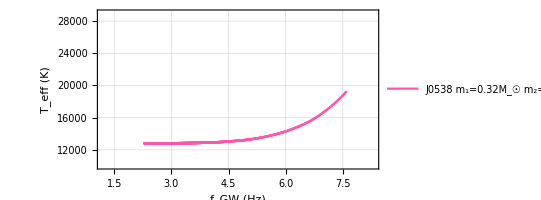

```mathematica
plota24lin=ListPlot[Transpose[{fvals2b[[;;RLposia]],10^4 Tvals2b[[;;RLposia]]}],Mesh->All,PlotMarkers->None,Joined-> True,PlotStyle-> Blend[{Magenta,Red,White}],PlotRange->{1000{0.0012,0.0083},{10000,29000}},AspectRatio->1/2,Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["f_GW (Hz)"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},GridLines->Automatic,PlotLegends->{Style["J0538 m_1=0.32M_☉ m_2=0.45M_☉ , Ω_0=0.32f_orb",16]}]
```

### together

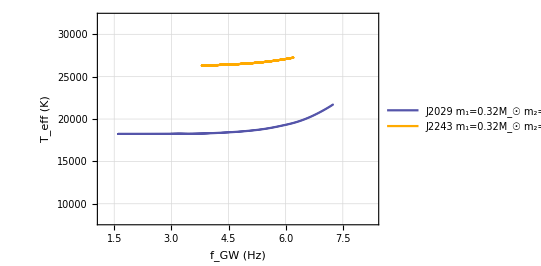

```mathematica
Show[plota21lin,plota23lin]
```

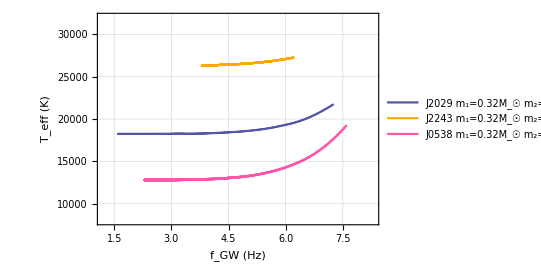

```mathematica
Show[plota21lin,plota23lin,plota24lin]
```